```mathematica
(*第一题 第1问*)
Clear["`*"]
q1z=ComplexExpand[-2/I+3I/(1+I)]
Re[q1z]
Im[q1z]
Abs[q1z]
Arg[q1z]
```

3/2+(7 ⅈ)/2

3/2

7/2

√(29/2)

ArcTan[7/3]

```mathematica
(*第一题 第2问*)
Clear["`*"]
q2=Solve[(1+2I)Conjugate[z]==4-3I,z]
Re[z/.q2]
Im[z/.q2]
Abs[z/.q2]
Arg[z/.q2]
```

{{z→-2/5+(11 ⅈ)/5}}

{-2/5}

{11/5}

{√5}

{π-ArcTan[11/2]}

```mathematica
(*第二题 第1问*)
Clear["`*"]
f[x,y]:=Exp[x]*(Cos[y]+I Sin[y])
u=FullSimplify[Re[f[x,y]],Assumptions->{x∈Reals,y∈Reals}]
v=FullSimplify[Im[f[x,y]],Assumptions->{x∈Reals,y∈Reals}]
dudx=FullSimplify[D[u,x]]
dudy=FullSimplify[D[u,y]]
dvdx=FullSimplify[D[v,x]]
dvdy=FullSimplify[D[v,y]]
dudx==dvdy&&dudy==-dvdx
```

ⅇ^x Cos[y]

ⅇ^x Sin[y]

ⅇ^x Cos[y]

-ⅇ^x Sin[y]

ⅇ^x Sin[y]

ⅇ^x Cos[y]

True

```mathematica
(*第二题 第2问*)
Clear["`*"]
f[x,y]:=(x^2-y^2+2x-3y)+I(2x y+3x+2y)
u=FullSimplify[Re[f[x,y]],Assumptions->{x∈Reals,y∈Reals}]
v=FullSimplify[Im[f[x,y]],Assumptions->{x∈Reals,y∈Reals}]
dudx=FullSimplify[D[u,x]]
dudy=FullSimplify[D[u,y]]
dvdx=FullSimplify[D[v,x]]
dvdy=FullSimplify[D[v,y]]
dudx==dvdy&&dudy==-dvdx
```

x (2+x)-y (3+y)

3 x+2 (1+x) y

2 (1+x)

-3-2 y

3+2 y

2 (1+x)

True

```mathematica
(*第三题 第1问*)
Clear["`*"]
f[n_]=1/n^2;
R=(Limit[Abs[f[n+1]/f[n]],n->Infinity])^(-1)
```

1

```mathematica
(*第三题 第2问*)
Clear["`*"]
f[n_]=n/3^n;
R=(Limit[Abs[f[n+1]/f[n]],n->Infinity])^(-1)
```

3

```mathematica
(*第四题 第1问*)
Clear["`*"]
f[x_]=Log[x+2];
Series[f[x],{x,0,10}]
```

Log[2]+x/2-x^2/8+x^3/24-x^4/64+x^5/160-x^6/384+x^7/896-x^8/2048+x^9/4608-x^10/10240+O[x]^11

```mathematica
(*第四题 第2问*)
Clear["`*"]
f[z_]=1/((z-1)(z-2));
(*易错，实际是在无穷远点展开,并不是下面的这种写法，原答案有误
Series[f[z],{z,0,10},Assumptions->(Abs[z]>2)]
*)
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+(63 z^5)/64+(127 z^6)/128+(255 z^7)/256+(511 z^8)/512+(1023 z^9)/1024+(2047 z^10)/2048+O[z]^11

```mathematica
(*正确写法*)
Clear["`*"]
f[z_]=1/((z-1)(z-2));
Series[f[z],{z,Infinity,10}]
```

(1/z)^2+3/z^3+7/z^4+15/z^5+31/z^6+63/z^7+127/z^8+255/z^9+511/z^10+O[1/z]^11

```mathematica
(*第五题 第1问*)
Clear["`*"]
(*易错，实际是在无穷远点展开,并不是下面的这种写法，原答案有误，少了dz的部分
Integrate[Exp[2*Exp[I*t]]/((2*Exp[I*t]+1)^2(2*Exp[I*t]-1)),{t,0,2Pi}]*)
(*正确写法*)
Integrate[Exp[2*Exp[I*t]]/((2*Exp[I*t]+1)^2(2*Exp[I*t]-1))*D[2*Exp[I*t],t],{t,0,2Pi}]
```

(ⅈ (-3+ⅇ^2) π)/(2 ⅇ)

```mathematica
(*第五题 第2问*)
Clear["`*"]
Integrate[Im[z],{z,0,2+I}]
```

1+ⅈ/2

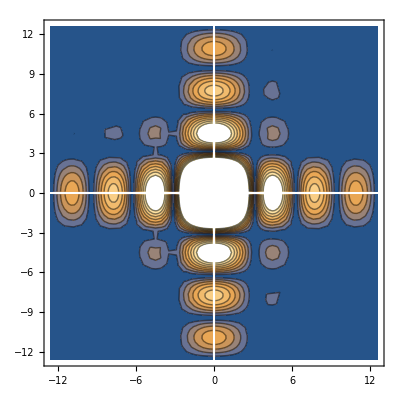

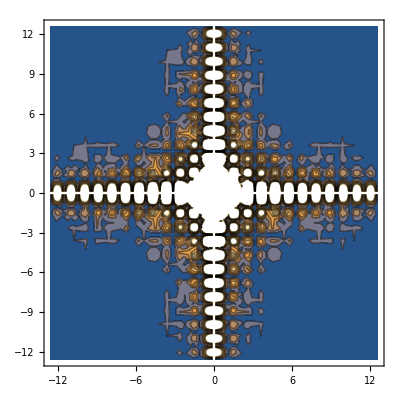

```mathematica
(*第六题*)
Clear["`*"]
f1[x,y]=Piecewise[{{2,Abs[x]<1&&Abs[y]<1}},0];
F1=FourierTransform[f1[x,y],{x,y},{u,v}];
ContourPlot[Abs[F1],{u,-4Pi,4Pi},{v,-4Pi,4Pi}]
f2[x,y]=Piecewise[{{2,Abs[x]<3&&Abs[y]<3}},0];
F2=FourierTransform[f2[x,y],{x,y},{u,v}];
ContourPlot[Abs[F2],{u,-4Pi,4Pi},{v,-4Pi,4Pi}]
```

Piecewise[{{-ⅇ^-x Sinh[x], x>0}, {0, True}}]

1/(w (-2 ⅈ+w))-1/2 π DiracDelta[w]

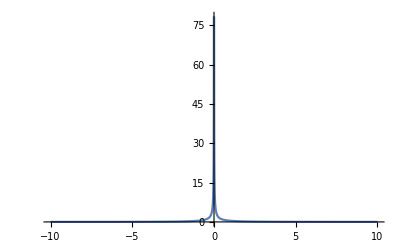

```mathematica
(*第七题*)
Clear["`*"]
f1=Piecewise[{{0,t<0}},-1];
f2=Piecewise[{{0,t<0}},Exp[-2t]];
f=Convolve[f1,f2,t,x]
F=FourierTransform[f,x,w,FourierParameters->{1,-1}]
Plot[Abs[F],{w,-10,10},PlotRange->All]
```

```mathematica
(*第八题*)
Clear["`*"]
f1=y''[t]+2y'[t]+3y[t];
f2=3Cos[t];
F1=LaplaceTransform[f1,t,s];
F2=LaplaceTransform[f2,t,s];
sol=Solve[F1==F2,LaplaceTransform[y[t],t,s]]/.{y[0]->0,y'[0]->1};
InverseLaplaceTransform[sol,s,t]
```

{{y[t]→3/4 (Cos[t]+Sin[t])-1/4 ⅇ^-t (3 Cos[√2 t]+√2 Sin[√2 t])}}

```mathematica
(*第九题*)
Clear["`*"]
f1=TriangleWave[{0,2},(x-1/2)/2];
F1=FourierSeries[f1,x,1];
F5=FourierSeries[f1,x,5];
F9=FourierSeries[f1,x,9];
```

```mathematica
Plot[{f1,F1,F5,F9},{x,-5,5},PlotLabels->{"f[x]","1阶展开","5阶展开","9阶展开"}]
```

-Graphics-

```mathematica
Clear["`*"] 
sol=NDSolve[{D[u[x,t],{t,2}]-D[u[x,t],{x,2}]==0,u[x,0]==Exp[-x^2],Derivative[0,1][u][x,0]==0,u[-6,t]==u[6,t]},u,{t,0,5},{x,-6,6}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[u[t,x]/. First[sol]],{t,0,2},{x,-6, 6}, PlotRange->All]
```

InterpolatingFunction::dmval: 输入值 {0.000143,-5.99914} 位于插值函数的数据范围之外. 将使用外推法.

-Graphics3D-